# Stark effect with Zeeman effect

This software calculates the Stark shift of Rydberg levels in presence of a bias magnetic field, which creates also a Zeeman shift.
The magnetic field is in general not aligned with the electric field, which creates different quantization directions. So one has to include also all the mJ inside (in the case without B, as the Stark interaction term couples levels with the same mL, and thus the same mJ, we could select just the levels with ΔmJ = 0).

The electric field points at the quantization direction of the atoms, the z direction; the magnetic field makes an angle α with the electric field, in the zx plane.

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.1311804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};


(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

{3.13118,2.65488,2.64167,1.34809,1.34647,0.0165192,0.0165437,0}

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",8,8]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267742

-0.0267742

0.00740212

{0.,0.00741686}

## | 60 p3/2, mj = 3/2 >

#### Selection of Hilbert basis for the calculation, centered at |60p3/2>

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=3/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=50; Subscript[n, max]=70;

δf=40*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Abs[Subscript[m, A]-Subscript[m, 1]]≤ 10,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.99956×10^11

{0.234,Null}

2406

{{57,3,5/2,-5/2,-1.01315×10^12,-1},{57,3,5/2,-3/2,-1.01315×10^12,-1},{57,3,5/2,-1/2,-1.01315×10^12,-1},{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,5/2,3/2,-1.01315×10^12,-1},{57,3,5/2,5/2,-1.01315×10^12,-1},{57,3,7/2,-7/2,-1.01315×10^12,-1},«2392»,{61,0,1/2,1/2,-9.8239×10^11,1},{61,1,1/2,-1/2,-9.66417×10^11,-1},{61,1,1/2,1/2,-9.66417×10^11,-1},{61,1,3/2,-3/2,-9.6598×10^11,-1},{61,1,3/2,-1/2,-9.6598×10^11,-1},{61,1,3/2,1/2,-9.6598×10^11,-1},{61,1,3/2,3/2,-9.6598×10^11,-1}}

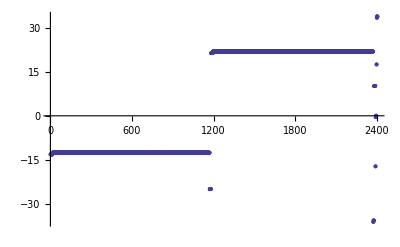

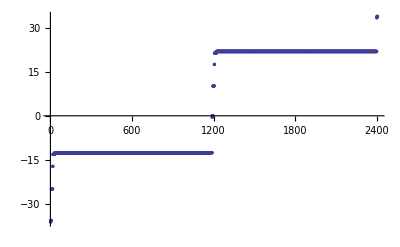

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

#### Creation of a list with the label of each level

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]
```

{59|1|1/2|-1/2,59|1|1/2|1/2,59|1|3/2|-3/2,59|1|3/2|-1/2,59|1|3/2|1/2,59|1|3/2|3/2,58|2|3/2|-3/2,58|2|3/2|-1/2,58|2|3/2|1/2,58|2|3/2|3/2,58|2|5/2|-5/2,58|2|5/2|-3/2,58|2|5/2|-1/2,58|2|5/2|1/2,58|2|5/2|3/2,58|2|5/2|5/2,60|0|1/2|-1/2,60|0|1/2|1/2,57|3|7/2|-7/2,57|3|7/2|-5/2,57|3|7/2|-3/2,57|3|7/2|-1/2,57|3|7/2|1/2,«2360»,58|57|113/2|3/2,58|57|113/2|5/2,58|57|113/2|7/2,58|57|113/2|9/2,58|57|113/2|11/2,58|57|113/2|13/2,58|57|115/2|-7/2,58|57|115/2|-5/2,58|57|115/2|-3/2,58|57|115/2|-1/2,58|57|115/2|1/2,58|57|115/2|3/2,58|57|115/2|5/2,58|57|115/2|7/2,58|57|115/2|9/2,58|57|115/2|11/2,58|57|115/2|13/2,61|1|1/2|-1/2,61|1|1/2|1/2,61|1|3/2|-3/2,61|1|3/2|-1/2,61|1|3/2|1/2,61|1|3/2|3/2}

#### Calculation of coupling between levels due to electric field (Stark effect)

```mathematica
(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

RDip[{1,0,1},{1,0,1}]

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]



(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

7.07037

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.27917,0.-4.27917 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, -7/2}, {1, -1}, {5/2, 5/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -7/2}, {1, 0}, {5/2, 5/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, -1}, {5/2, 5/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, 1}, {5/2, 5/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, -1}, {5/2, 5/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{292.861,Null}

{0,0,0}

#### Calculation of coupling between levels due to magnetic field (Zeeman effect)

```mathematica
(*Calculation of Zeeman term <n,l,j,m| μ*B |np,lp,jp,mp> *)

Bfield = 8.71*10^(-4); (* Magnetic field in Tesla *)
α = Pi/2; (* angle between electric field and magnetic field, in radians *)

RZeeman [{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,0];
RZeeman [{60,0,1},{60,0,1}]
RZeeman [{100,0,1},{100,0,1}]
RZeeman [{60,0,1},{59,0,1}]
RZeeman [{60,1,3},{60,1,3}]
RZeeman [{60,1,3},{59,1,3}]

(*Landé g-factor*)
g[l_,j_] := 3/2+(3/4-l*(l+1))/(2*j*(j+1));

g[0,1/2]
g[1,3/2]
BMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_},α_]:=RZeeman [{np,lp,Chooselj[lp,jp]},{n,l,Chooselj[l,j]}]  *  g[lp,jp]* KroneckerDelta[lp,l]*KroneckerDelta[jp,j]* (Cos[α]*mp*KroneckerDelta[mp,m]+Sin[α]/2*(Sqrt[jp*(jp+1)-mp*(mp+1)]*KroneckerDelta[mp+1,m]+Sqrt[jp*(jp+1)-mp*(mp-1)]*KroneckerDelta[mp-1,m])  );

BMatrixelement[{60,0,1/2,1/2},{60,0,1/2,1/2},0]*Subscript[μ, B]/h/10^9*10^(-4) (*Zeeman effect, GHz per Gauss, for s fine levels *)
BMatrixelement[{60,1,3/2,3/2},{60,1,3/2,3/2},0]*Subscript[μ, B]/h/10^9*10^(-4)  (*Zeeman effect, GHz per Gauss, for p 3/2 fine levels *)



(*Fill up Matrix with  <A|μ*B|A'>  *)
Clear[AI]
BMatrix=Array[B,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[ (NList[[i,2]]==NList[[k,2]])&&(NList[[i,3]]==NList[[k,3]]) ,
BMatrix[[i,k]]=BMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]},α],
BMatrix[[i,k]]=0;]]
] 
] 

Clear[i,k,AI]

MatrixPlot[BMatrix]
```

1.

1.

-0.000405891

1.

-0.00041805

2

4/3

0.00139962

0.00279925

{59.952,Null}

-Graphics-

#### Calculation of free energies for each level (without interaction): the diagonal terms of the Hamiltonian in absence of magnetic field

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.02504×10^12,-1.02504×10^12,-1.02504×10^12,-1.02504×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.03624×10^12,-1.03624×10^12,-1.03576×10^12,-1.03576×10^12,-1.03576×10^12,-1.03576×10^12,-9.89788×10^11,-9.89788×10^11,-9.89788×10^11,-9.89788×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-1.01724×10^12,-1.01724×10^12,-1.00042×10^12,-1.00042×10^12,-9.99956×10^11,-9.99956×10^11,-9.99956×10^11,-9.99956×10^11,-9.8239×10^11,-9.8239×10^11,-9.66417×10^11,-9.66417×10^11,-9.6598×10^11,-9.6598×10^11,-9.6598×10^11,-9.6598×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9]
```

-Graphics-

-Graphics-

-Graphics-

{-1036.25,-1036.24,-1035.78,-1035.76,-1035.75,-1035.73,-1025.05,-1025.04,-1025.03,-1025.02,-1025.02,-1025.,-1024.99,-1024.97,-1024.96,-1024.94,-1017.26,-1017.23,-1013.24,-1013.23,-1013.22,-1013.22,-1013.21,-1013.21,-1013.2,-1013.2,-1013.2,-1013.19,-1013.18,-1013.18,-1013.18,-1013.17,-1013.17,-1013.17,-1013.17,-1013.17,-1013.16,-1013.16,-1013.16,-1013.16,-1013.16,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.14,-1013.14,-1013.14,-1013.14,-1013.14,-1013.13,-1013.13,-1013.13,-1013.13,-1013.13,-1013.13,-1013.12,-1013.12,-1013.12,-1013.11,-1013.11,-1013.11,-1013.11,-1013.1,-1013.1,-1013.1,-1013.1,-1013.1,-1013.09,-1013.09,-1013.09,-1013.09,-1013.08,-1013.08,-1013.08,-1013.08,-1013.07,-1013.07,-1013.07,-1013.07,-1013.06,-1013.06,-1013.06,-1013.05,-1013.05,-1013.05,-1013.05,-1013.05,-1013.05,-1013.05,-1013.04,-1013.04,-1013.04,-1013.04,-1013.04,-1013.04,-1013.03,-1013.03,-1013.03,-1013.03,-1013.02,-1013.02,-1013.02,-1013.02,-1013.02,-1013.02,-1013.01,-1013.01,-1013.01,-1013.01,-1013.01,-1013.01,-1013.,-1013.,-1013.,-1013.,-1012.99,-1012.99,-1012.99,-1012.99,-1012.99,-1012.99,-1012.98,-1012.98,-1012.98,-1012.98,-1012.98,-1012.98,-1012.98,-1012.98,-1012.97,-1012.97,-1012.97,-1012.97,-1012.97,-1012.97,-1012.96,-1012.96,-1012.96,-1012.96,-1012.96,-1012.96,-1012.95,-1012.95,-1012.95,-1012.95,-1012.95,-1012.95,-1012.94,-1012.94,-1012.94,-1012.94,-1012.94,-1012.94,-1012.93,-1012.93,-1012.93,-1012.93,-1012.92,-1012.92,-1012.92,-1012.92,-1012.92,-1012.92,-1012.92,-1012.91,-1012.91,-1012.91,-1012.91,-1012.91,-1012.91,-1012.91,-1012.91,-1012.91,-1012.91,-1012.91,-1012.9,-1012.9,-1012.9,-1012.9,-1012.9,-1012.9,-1012.9,-1012.9,-1012.89,-1012.89,-1012.89,-1012.89,-1012.89,-1012.89,-1012.89,-1012.89,-1012.89,-1012.89,-1012.88,-1012.88,-1012.88,-1012.88,-1012.88,-1012.88,-1012.88,-1012.88,-1012.88,-1012.87,-1012.87,-1012.87,-1012.87,-1012.87,-1012.86,-1012.86,-1012.86,-1012.86,-1012.86,-1012.86,-1012.86,-1012.86,-1012.86,-1012.86,-1012.85,-1012.85,-1012.85,-1012.85,-1012.85,-1012.85,-1012.85,-1012.85,-1012.85,-1012.84,-1012.84,-1012.84,-1012.84,-1012.84,-1012.84,-1012.84,-1012.84,-1012.84,-1012.84,-1012.84,-1012.83,-1012.83,-1012.83,-1012.83,-1012.83,-1012.83,-1012.83,-1012.83,-1012.83,-1012.83,-1012.82,-1012.82,-1012.82,-1012.82,-1012.82,-1012.82,-1012.82,-1012.82,-1012.81,-1012.81,-1012.81,-1012.81,-1012.81,-1012.81,-1012.81,-1012.81,-1012.81,-1012.8,-1012.8,-1012.8,-1012.8,-1012.8,-1012.8,-1012.8,-1012.8,-1012.8,-1012.79,-1012.79,-1012.79,-1012.79,-1012.79,-1012.79,-1012.79,-1012.79,-1012.78,-1012.78,-1012.78,-1012.78,-1012.78,-1012.78,-1012.78,-1012.78,-1012.78,-1012.78,-1012.77,-1012.77,-1012.77,-1012.77,-1012.77,-1012.77,-1012.77,-1012.77,-1012.77,-1012.77,-1012.76,-1012.76,-1012.76,-1012.76,-1012.76,-1012.76,-1012.76,-1012.76,-1012.76,-1012.76,-1012.76,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.75,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.74,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.73,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.72,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.71,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.7,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.69,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.68,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.67,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.66,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.65,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.64,-1012.63,-1012.63,-1012.63,-1012.63,-1012.63,-1012.63,-1012.63,-1012.63,-1012.63,-1012.63,-1012.63,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.5,-1012.49,-1012.49,-1012.49,-1012.49,-1012.49,-1012.49,-1012.49,-1012.49,-1012.49,-1012.49,-1012.49,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.48,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.47,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.46,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.45,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.44,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.43,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.42,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.41,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.4,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.39,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.38,-1012.37,-1012.37,-1012.37,-1012.37,-1012.37,-1012.37,-1012.37,-1012.37,-1012.37,-1012.36,-1012.36,-1012.36,-1012.36,-1012.36,-1012.36,-1012.36,-1012.36,-1012.36,-1012.36,-1012.35,-1012.35,-1012.35,-1012.35,-1012.35,-1012.35,-1012.35,-1012.35,-1012.35,-1012.35,-1012.35,-1012.34,-1012.34,-1012.34,-1012.34,-1012.34,-1012.34,-1012.34,-1012.34,-1012.34,-1012.33,-1012.33,-1012.33,-1012.33,-1012.33,-1012.33,-1012.33,-1012.33,-1012.32,-1012.32,-1012.32,-1012.32,-1012.32,-1012.32,-1012.32,-1012.32,-1012.31,-1012.31,-1012.31,-1012.31,-1012.31,-1012.31,-1012.31,-1012.31,-1012.31,-1012.31,-1012.3,-1012.3,-1012.3,-1012.3,-1012.3,-1012.3,-1012.3,-1012.3,-1012.3,-1012.3,-1012.29,-1012.29,-1012.29,-1012.29,-1012.29,-1012.29,-1012.29,-1012.29,-1012.28,-1012.28,-1012.28,-1012.28,-1012.28,-1012.28,-1012.28,-1012.28,-1012.28,-1012.27,-1012.27,-1012.27,-1012.27,-1012.27,-1012.27,-1012.27,-1012.26,-1012.26,-1012.26,-1012.26,-1012.26,-1012.26,-1012.26,-1012.26,-1012.26,-1012.26,-1012.25,-1012.25,-1012.25,-1012.25,-1012.25,-1012.25,-1012.25,-1012.25,-1012.25,-1012.25,-1012.24,-1012.24,-1012.24,-1012.24,-1012.24,-1012.24,-1012.24,-1012.24,-1012.23,-1012.23,-1012.23,-1012.23,-1012.23,-1012.23,-1012.23,-1012.23,-1012.23,-1012.23,-1012.22,-1012.22,-1012.22,-1012.22,-1012.22,-1012.22,-1012.22,-1012.22,-1012.22,-1012.21,-1012.21,-1012.21,-1012.21,-1012.21,-1012.21,-1012.2,-1012.2,-1012.2,-1012.2,-1012.2,-1012.2,-1012.2,-1012.19,-1012.19,-1012.19,-1012.19,-1012.19,-1012.19,-1012.18,-1012.18,-1012.18,-1012.18,-1012.18,-1012.18,-1012.17,-1012.17,-1012.17,-1012.17,-1012.17,-1012.17,-1012.16,-1012.16,-1012.16,-1012.16,-1012.16,-1012.16,-1012.15,-1012.15,-1012.15,-1012.15,-1012.15,-1012.15,-1012.14,-1012.14,-1012.14,-1012.14,-1012.14,-1012.14,-1012.13,-1012.13,-1012.13,-1012.13,-1012.13,-1012.13,-1012.12,-1012.12,-1012.12,-1012.12,-1012.11,-1012.11,-1012.11,-1012.11,-1012.11,-1012.11,-1012.1,-1012.1,-1012.1,-1012.1,-1012.1,-1012.1,-1012.09,-1012.09,-1012.09,-1012.09,-1012.09,-1012.09,-1012.08,-1012.08,-1012.08,-1012.08,-1012.07,-1012.07,-1012.07,-1012.07,-1012.07,-1012.07,-1012.06,-1012.06,-1012.06,-1012.06,-1012.05,-1012.05,-1012.05,-1012.05,-1012.04,-1012.04,-1012.04,-1012.04,-1012.03,-1012.03,-1012.03,-1012.03,-1012.02,-1012.02,-1012.02,-1012.02,-1012.01,-1012.01,-1012.,-1012.,-1012.,-1012.,-1011.99,-1011.99,-1011.99,-1011.99,-1011.98,-1011.98,-1011.98,-1011.98,-1011.97,-1011.97,-1011.97,-1011.96,-1011.96,-1011.96,-1011.94,-1011.94,-1011.93,-1011.93,-1011.92,-1011.92,-1011.91,-1011.91,-1011.9,-1011.88,-1000.42,-1000.41,-999.98,-999.964,-999.948,-999.931,-989.803,-989.793,-989.783,-989.773,-989.769,-989.754,-989.74,-989.725,-989.71,-989.696,-982.402,-982.378,-978.64,-978.629,-978.617,-978.617,-978.605,-978.605,-978.593,-978.593,-978.581,-978.581,-978.57,-978.569,-978.569,-978.558,-978.558,-978.558,-978.557,-978.548,-978.548,-978.546,-978.546,-978.543,-978.537,-978.537,-978.534,-978.534,-978.533,-978.529,-978.527,-978.527,-978.523,-978.522,-978.522,-978.516,-978.516,-978.515,-978.512,-978.51,-978.51,-978.505,-978.505,-978.502,-978.501,-978.498,-978.498,-978.495,-978.495,-978.491,-978.487,-978.487,-978.487,-978.484,-978.484,-978.481,-978.475,-978.475,-978.474,-978.473,-978.473,-978.463,-978.463,-978.463,-978.463,-978.459,-978.457,-978.452,-978.452,-978.451,-978.451,-978.448,-978.442,-978.441,-978.439,-978.439,-978.439,-978.439,-978.431,-978.431,-978.431,-978.43,-978.427,-978.427,-978.422,-978.422,-978.42,-978.42,-978.416,-978.415,-978.413,-978.413,-978.41,-978.409,-978.405,-978.404,-978.404,-978.404,-978.399,-978.399,-978.396,-978.396,-978.392,-978.392,-978.388,-978.388,-978.387,-978.387,-978.38,-978.38,-978.378,-978.378,-978.378,-978.377,-978.37,-978.369,-978.368,-978.368,-978.367,-978.367,-978.361,-978.361,-978.356,-978.356,-978.356,-978.356,-978.352,-978.352,-978.346,-978.345,-978.344,-978.344,-978.344,-978.343,-978.335,-978.335,-978.335,-978.335,-978.333,-978.332,-978.326,-978.326,-978.324,-978.324,-978.321,-978.321,-978.317,-978.317,-978.314,-978.313,-978.311,-978.309,-978.309,-978.309,-978.308,-978.305,-978.303,-978.303,-978.3,-978.3,-978.299,-978.298,-978.297,-978.297,-978.292,-978.292,-978.292,-978.292,-978.291,-978.291,-978.286,-978.286,-978.285,-978.285,-978.282,-978.282,-978.282,-978.281,-978.28,-978.28,-978.274,-978.274,-978.274,-978.273,-978.273,-978.273,-978.271,-978.271,-978.268,-978.267,-978.265,-978.265,-978.261,-978.261,-978.261,-978.261,-978.26,-978.26,-978.256,-978.256,-978.255,-978.255,-978.25,-978.249,-978.249,-978.249,-978.249,-978.249,-978.247,-978.247,-978.243,-978.243,-978.239,-978.239,-978.239,-978.238,-978.238,-978.237,-978.237,-978.236,-978.23,-978.23,-978.23,-978.23,-978.228,-978.228,-978.226,-978.225,-978.224,-978.224,-978.221,-978.221,-978.218,-978.218,-978.217,-978.217,-978.214,-978.214,-978.212,-978.212,-978.212,-978.211,-978.207,-978.206,-978.205,-978.205,-978.204,-978.203,-978.202,-978.202,-978.199,-978.199,-978.196,-978.196,-978.195,-978.195,-978.193,-978.193,-978.19,-978.19,-978.187,-978.186,-978.186,-978.186,-978.185,-978.185,-978.181,-978.18,-978.178,-978.178,-978.177,-978.177,-978.174,-978.174,-978.174,-978.174,-978.169,-978.168,-978.168,-978.168,-978.166,-978.166,-978.164,-978.163,-978.162,-978.161,-978.16,-978.159,-978.156,-978.155,-978.154,-978.154,-978.153,-978.152,-978.151,-978.15,-978.149,-978.149,-978.144,-978.143,-978.143,-978.143,-978.142,-978.142,-978.142,-978.142,-978.141,-978.141,-978.138,-978.138,-978.137,-978.136,-978.135,-978.134,-978.133,-978.133,-978.131,-978.131,-978.131,-978.131,-978.13,-978.13,-978.13,-978.13,-978.128,-978.128,-978.125,-978.124,-978.124,-978.124,-978.124,-978.124,-978.121,-978.121,-978.12,-978.119,-978.118,-978.118,-978.118,-978.118,-978.118,-978.117,-978.115,-978.115,-978.114,-978.114,-978.112,-978.111,-978.111,-978.111,-978.109,-978.108,-978.108,-978.107,-978.107,-978.106,-978.106,-978.105,-978.105,-978.105,-978.104,-978.104,-978.101,-978.101,-978.099,-978.099,-978.098,-978.098,-978.097,-978.097,-978.097,-978.096,-978.095,-978.094,-978.094,-978.094,-978.093,-978.092,-978.091,-978.09,-978.088,-978.088,-978.087,-978.087,-978.087,-978.086,-978.086,-978.086,-978.084,-978.084,-978.083,-978.082,-978.081,-978.08,-978.08,-978.079,-978.079,-978.078,-978.077,-978.077,-978.076,-978.075,-978.074,-978.074,-978.073,-978.073,-978.071,-978.071,-978.07,-978.07,-978.069,-978.068,-978.067,-978.067,-978.067,-978.066,-978.065,-978.064,-978.063,-978.063,-978.061,-978.06,-978.06,-978.06,-978.059,-978.059,-978.058,-978.057,-978.056,-978.055,-978.054,-978.054,-978.053,-978.053,-978.052,-978.052,-978.05,-978.05,-978.049,-978.048,-978.047,-978.046,-978.046,-978.046,-978.045,-978.043,-978.043,-978.042,-978.041,-978.04,-978.04,-978.039,-978.039,-978.039,-978.038,-978.036,-978.036,-978.035,-978.034,-978.033,-978.032,-978.032,-978.031,-978.031,-978.029,-978.028,-978.028,-978.027,-978.026,-978.025,-978.024,-978.024,-978.022,-978.022,-978.021,-978.021,-978.019,-978.019,-978.018,-978.017,-978.016,-978.016,-978.015,-978.013,-978.013,-978.012,-978.011,-978.009,-978.009,-978.009,-978.008,-978.007,-978.007,-978.006,-978.006,-978.006,-978.005,-978.004,-978.004,-978.003,-978.003,-978.002,-978.002,-978.001,-978.001,-978.,-978.,-977.999,-977.999,-977.999,-977.998,-977.997,-977.997,-977.997,-977.996,-977.996,-977.995,-977.994,-977.993,-977.993,-977.992,-977.992,-977.991,-977.991,-977.99,-977.99,-977.989,-977.989,-977.988,-977.988,-977.987,-977.987,-977.986,-977.986,-977.984,-977.984,-977.984,-977.983,-977.982,-977.982,-977.982,-977.981,-977.98,-977.98,-977.979,-977.979,-977.978,-977.978,-977.977,-977.977,-977.977,-977.976,-977.975,-977.975,-977.974,-977.974,-977.973,-977.973,-977.973,-977.972,-977.972,-977.971,-977.971,-977.97,-977.969,-977.969,-977.968,-977.968,-977.967,-977.967,-977.966,-977.966,-977.966,-977.965,-977.965,-977.964,-977.963,-977.963,-977.962,-977.961,-977.961,-977.96,-977.96,-977.959,-977.959,-977.959,-977.958,-977.957,-977.957,-977.957,-977.956,-977.955,-977.955,-977.955,-977.954,-977.954,-977.953,-977.953,-977.953,-977.952,-977.952,-977.952,-977.951,-977.95,-977.95,-977.949,-977.948,-977.948,-977.947,-977.947,-977.946,-977.946,-977.946,-977.945,-977.945,-977.944,-977.944,-977.944,-977.943,-977.943,-977.942,-977.941,-977.941,-977.941,-977.94,-977.939,-977.939,-977.939,-977.939,-977.938,-977.938,-977.937,-977.937,-977.935,-977.935,-977.934,-977.934,-977.933,-977.933,-977.932,-977.932,-977.932,-977.931,-977.93,-977.93,-977.93,-977.929,-977.928,-977.928,-977.927,-977.927,-977.926,-977.926,-977.925,-977.925,-977.925,-977.924,-977.923,-977.923,-977.922,-977.922,-977.921,-977.921,-977.921,-977.921,-977.92,-977.919,-977.919,-977.919,-977.918,-977.917,-977.916,-977.916,-977.915,-977.914,-977.914,-977.914,-977.913,-977.912,-977.911,-977.911,-977.91,-977.91,-977.91,-977.909,-977.909,-977.908,-977.908,-977.907,-977.907,-977.906,-977.906,-977.905,-977.904,-977.904,-977.903,-977.902,-977.902,-977.901,-977.901,-977.9,-977.899,-977.899,-977.899,-977.898,-977.898,-977.897,-977.897,-977.896,-977.896,-977.895,-977.895,-977.894,-977.894,-977.893,-977.893,-977.892,-977.892,-977.892,-977.891,-977.89,-977.89,-977.89,-977.889,-977.888,-977.886,-977.885,-977.885,-977.883,-977.883,-977.882,-977.881,-977.881,-977.879,-977.879,-977.878,-977.877,-977.877,-977.876,-977.875,-977.874,-977.874,-977.873,-977.871,-977.87,-977.87,-977.87,-977.868,-977.867,-977.867,-977.866,-977.866,-977.865,-977.863,-977.863,-977.863,-977.86,-977.86,-977.86,-977.859,-977.858,-977.858,-977.858,-977.856,-977.855,-977.855,-977.854,-977.853,-977.852,-977.852,-977.852,-977.85,-977.849,-977.848,-977.848,-977.847,-977.846,-977.845,-977.845,-977.845,-977.844,-977.843,-977.842,-977.841,-977.841,-977.84,-977.839,-977.839,-977.839,-977.838,-977.838,-977.835,-977.835,-977.835,-977.834,-977.833,-977.832,-977.832,-977.831,-977.83,-977.829,-977.829,-977.828,-977.828,-977.828,-977.826,-977.825,-977.825,-977.824,-977.824,-977.823,-977.821,-977.821,-977.821,-977.82,-977.819,-977.819,-977.818,-977.818,-977.817,-977.816,-977.815,-977.814,-977.813,-977.813,-977.812,-977.812,-977.811,-977.811,-977.811,-977.81,-977.808,-977.808,-977.806,-977.806,-977.805,-977.804,-977.804,-977.804,-977.802,-977.801,-977.801,-977.801,-977.801,-977.8,-977.8,-977.799,-977.798,-977.797,-977.794,-977.794,-977.794,-977.793,-977.793,-977.792,-977.792,-977.792,-977.791,-977.791,-977.79,-977.789,-977.788,-977.787,-977.787,-977.787,-977.784,-977.784,-977.784,-977.783,-977.781,-977.781,-977.781,-977.781,-977.78,-977.78,-977.779,-977.778,-977.778,-977.777,-977.775,-977.775,-977.774,-977.774,-977.774,-977.774,-977.771,-977.77,-977.769,-977.768,-977.768,-977.768,-977.768,-977.768,-977.767,-977.767,-977.766,-977.765,-977.764,-977.764,-977.762,-977.762,-977.761,-977.76,-977.757,-977.757,-977.757,-977.757,-977.756,-977.756,-977.756,-977.756,-977.755,-977.754,-977.749,-977.749,-977.748,-977.748,-977.746,-977.746,-977.744,-977.744,-977.743,-977.743,-977.739,-977.739,-977.737,-977.737,-977.735,-977.735,-977.733,-977.732,-977.731,-977.73,-977.73,-977.73,-977.725,-977.724,-977.724,-977.724,-977.721,-977.721,-977.721,-977.72,-977.718,-977.718,-977.714,-977.713,-977.713,-977.712,-977.712,-977.712,-977.709,-977.708,-977.706,-977.705,-977.704,-977.704,-977.703,-977.703,-977.7,-977.699,-977.697,-977.697,-977.695,-977.695,-977.693,-977.693,-977.692,-977.692,-977.687,-977.687,-977.686,-977.686,-977.685,-977.685,-977.681,-977.681,-977.681,-977.681,-977.678,-977.677,-977.675,-977.674,-977.673,-977.673,-977.671,-977.67,-977.669,-977.668,-977.668,-977.668,-977.662,-977.662,-977.661,-977.661,-977.66,-977.66,-977.66,-977.66,-977.656,-977.656,-977.651,-977.651,-977.65,-977.649,-977.649,-977.649,-977.649,-977.649,-977.643,-977.643,-977.642,-977.642,-977.638,-977.638,-977.637,-977.637,-977.637,-977.637,-977.634,-977.633,-977.631,-977.631,-977.628,-977.627,-977.625,-977.625,-977.625,-977.625,-977.625,-977.625,-977.619,-977.618,-977.617,-977.617,-977.616,-977.616,-977.614,-977.613,-977.612,-977.612,-977.607,-977.607,-977.606,-977.606,-977.606,-977.606,-977.602,-977.601,-977.6,-977.6,-977.599,-977.599,-977.596,-977.595,-977.594,-977.59,-977.59,-977.59,-977.59,-977.588,-977.585,-977.585,-977.581,-977.581,-977.578,-977.578,-977.574,-977.574,-977.573,-977.572,-977.566,-977.566,-977.564,-977.564,-977.564,-977.563,-977.555,-977.555,-977.554,-977.554,-977.553,-977.553,-977.546,-977.546,-977.542,-977.542,-977.542,-977.542,-977.538,-977.537,-977.532,-977.531,-977.53,-977.53,-977.529,-977.529,-977.521,-977.521,-977.52,-977.52,-977.519,-977.518,-977.512,-977.511,-977.51,-977.51,-977.507,-977.507,-977.503,-977.503,-977.5,-977.499,-977.495,-977.495,-977.494,-977.494,-977.489,-977.489,-977.485,-977.485,-977.483,-977.483,-977.478,-977.478,-977.477,-977.476,-977.471,-977.471,-977.468,-977.468,-977.468,-977.467,-977.459,-977.459,-977.459,-977.459,-977.457,-977.457,-977.451,-977.447,-977.447,-977.446,-977.446,-977.442,-977.436,-977.436,-977.436,-977.435,-977.425,-977.425,-977.424,-977.424,-977.414,-977.414,-977.412,-977.412,-977.404,-977.404,-977.4,-977.4,-977.393,-977.393,-977.388,-977.388,-977.383,-977.382,-977.376,-977.376,-977.372,-977.372,-977.365,-977.364,-977.361,-977.361,-977.353,-977.353,-977.351,-977.35,-977.341,-977.341,-977.34,-977.329,-977.329,-977.329,-977.317,-977.317,-977.305,-977.305,-977.293,-977.293,-977.282,-977.282,-977.27,-977.258,-966.421,-966.413,-966.004,-965.988,-965.971,-965.955}

{{10,-36.2935,59|1|1/2|-1/2},{10,-36.2935,59|1|1/2|1/2},{10,-35.81,59|1|3/2|-3/2},{10,-35.81,59|1|3/2|-1/2},{10,-35.8064,59|1|3/2|1/2},{10,-35.8064,59|1|3/2|3/2},{10,-25.0864,58|2|3/2|-3/2},{10,-25.0864,58|2|3/2|-1/2},«2390»,{10,22.6308,58|57|115/2|11/2},{10,22.6308,58|57|115/2|13/2},{10,33.5414,61|1|1/2|-1/2},{10,33.5414,61|1|1/2|1/2},{10,33.977,61|1|3/2|-3/2},{10,33.977,61|1|3/2|-1/2},{10,33.9805,61|1|3/2|1/2},{10,33.9805,61|1|3/2|3/2}}

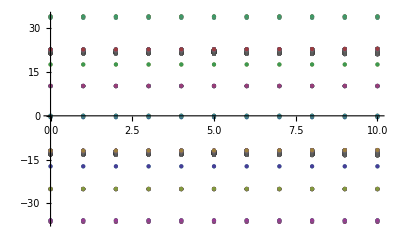

ListPlot::lpn: MPL123221321ist is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

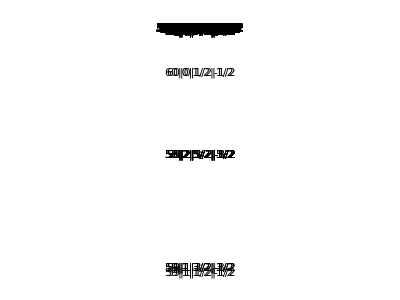
Show[ListPlot[MPL123221321ist,Joined→True,PlotRange→{All,{-100,100}},Frame→True],-Graphics-]

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=-1;
EMAX=10;
ELabel=10;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;


For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPL123221321ist,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

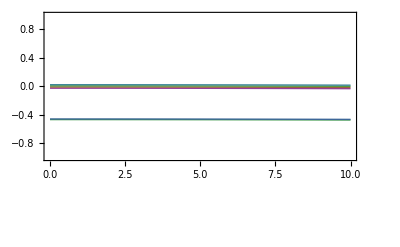

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[218]]

MPList[[218]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=Re[MPList[[i,j,2]]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60p3_2_mj3_2_with_B.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60p3_2_mj3_2.dat",Efieldlist]

(*Export["60p_j3_2_mj3_2_stark_Shift.dat",MPList[[218]]]*)
```

57|12|25/2|7/2

{{0,-12.9034-6.61706×10^-14 ⅈ},{1,-12.9066},{2,-12.9128},{3,-12.923},{4,-12.9392},{5,-12.9592},{6,-12.985},{7,-13.0095},{8,-13.0369},{9,-13.0669},{10,-13.0979}}

{0,1,2,3,4,5,6,7,8,9,10}

{{-36.2904,-36.2905,-36.2907,-36.2911,-36.2916,-36.2922,-36.293,-36.2939,-36.295,-36.2962,-36.2976},«2404»,{34.0004,34.0005,34.0006,34.0007,34.001,34.0013,34.0017,34.0022,34.0027,34.0033,34.004}}

Stark_Shifts_around_60p3_2_mj3_2_with_B.dat

Electric_fields_for_Stark_Shifts_around_60p3_2_mj3_2.dat

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

59|1|1/2|1/2

59|1|3/2|1/2

{{1,-18.999},{2,-18.9992},{3,-18.9994},{4,-18.9998},{5,-19.0002},{6,-19.0008},{7,-19.0014},{8,-19.0022},{9,-19.003},{10,-19.004},{11,-19.005},{12,-19.0062},{13,-19.0074},{14,-19.0088},{15,-19.0102},{16,-19.0117},{17,-19.0134},{18,-19.0151},{19,-19.017},{20,-19.0189},{21,-19.021},{22,-19.0231},{23,-19.0253},{24,-19.0277},{25,-19.0301},{26,-19.0326},{27,-19.0353},{28,-19.038},{29,-19.0408},{30,-19.0438},{31,-19.0468},{32,-19.0499},{33,-19.0532},{34,-19.0565},{35,-19.0599},{36,-19.0634},{37,-19.067},{38,-19.0707},{39,-19.0746},{40,-19.0785},{41,-19.0825},{42,-19.0866},{43,-19.0908},{44,-19.0951},{45,-19.0995},{46,-19.104},{47,-19.1086},{48,-19.1133},{49,-19.118},{50,-19.1229},{51,-19.1279},{52,-19.133},{53,-19.1381},{54,-19.1434},{55,-19.1488},{56,-19.1542},{57,-19.1598},{58,-19.1654},{59,-19.1712},{60,-19.177},{61,-19.1829},{62,-19.189},{63,-19.1951},{64,-19.2013},{65,-19.2076},{66,-19.214},{67,-19.2205},{68,-19.2271},{69,-19.2338},{70,-19.2405},{71,-19.2474},{72,-19.2544},{73,-19.2614},{74,-19.2685},{75,-19.2758},{76,-19.2831},{77,-19.2905},{78,-19.298},{79,-19.3056},{80,-19.3133},{81,-19.3211},{82,-19.329},{83,-19.3369},{84,-19.345},{85,-19.3531},{86,-19.3613},{87,-19.3697},{88,-19.3781},{89,-19.3866},{90,-19.3951},{91,-19.4038},{92,-19.4126},{93,-19.4214},{94,-19.4303},{95,-19.4394},{96,-19.4485},{97,-19.4577},{98,-19.4669},{99,-19.4763},{100,-19.4857},{101,-19.4953},{102,-19.5049},{103,-19.5146},{104,-19.5243},{105,-19.5342},{106,-19.5441},{107,-19.5542},{108,-19.5643},{109,-19.5745},{110,-19.5847},{111,-19.5951},{112,-19.6055},{113,-19.616},{114,-19.6266},{115,-19.6373},{116,-19.648},{117,-19.6589},{118,-19.6698},{119,-19.6807},{120,-19.6918},{121,-19.7029},{122,-19.7141},{123,-19.7254},{124,-19.7368},{125,-19.7482},{126,-19.7597},{127,-19.7713},{128,-19.783},{129,-19.7947},{130,-19.8065},{131,-19.8184},{132,-19.8303},{133,-19.8423},{134,-19.8544},{135,-19.8665},{136,-19.8788},{137,-19.891},{138,-19.9034},{139,-19.9158},{140,-19.9283},{141,-19.9409},{142,-19.9535},{143,-19.9662},{144,-19.9789},{145,-19.9917},{146,-20.0046},{147,-20.0175},{148,-20.0305},{149,-20.0436},{150,-20.0567},{151,-20.0698},{152,-20.0831},{153,-20.0964},{154,-20.1097},{155,-20.1231},{156,-20.1366},{157,-20.1501},{158,-20.1636},{159,-20.1772},{160,-20.1909},{161,-20.2046},{162,-20.2184},{163,-20.2322},{164,-20.2461},{165,-20.26},{166,-20.2739},{167,-20.2879},{168,-20.3019},{169,-20.316},{170,-20.3301},{171,-20.3443},{172,-20.3585},{173,-20.3727},{174,-20.387},{175,-20.4012},{176,-20.4155},{177,-20.4299},{178,-20.4442},{179,-20.4586},{180,-20.473},{181,-20.4874},{182,-20.5017},{183,-20.5161},{184,-20.5304},{185,-20.5448},{186,-20.559},{187,-20.5732},{188,-20.5872},{189,-20.601},{190,-20.6146},{191,-20.6275},{192,-20.6395},{193,-20.649},{194,-20.6514},{195,-20.6326},{196,-20.5911},{197,-20.5428},{198,-20.4972},{199,-20.466},{200,-20.4319},{201,-20.3832},{202,-20.3301},{203,-20.2757},{204,-20.2208},{205,-20.1657},{206,-20.1104},{207,-20.055},{208,-19.9996},{209,-19.9441},{210,-19.8886},{211,-19.8331},{212,-19.7775},{213,-19.722},{214,-19.6665},{215,-19.6109},{216,-19.5554},{217,-19.4999},{218,-19.4443},{219,-19.3888},{220,-19.3333},{221,-19.2778},{222,-19.2223},{223,-19.1668},{224,-19.1113},{225,-19.0559},{226,-19.0004},{227,-18.9449},{228,-18.8895},{229,-18.8341},{230,-18.7786},{231,-18.7232},{232,-18.6678},{233,-18.6124},{234,-18.557},{235,-18.5016},{236,-18.4463},{237,-18.3909},{238,-18.3356},{239,-18.2802},{240,-18.2249},{241,-18.1696},{242,-18.1143},{243,-18.059},{244,-18.0037},{245,-17.9484},{246,-17.8932},{247,-17.8379},{248,-17.7827},{249,-17.7274},{250,-17.6722},{251,-17.617},{252,-17.5618},{253,-17.5066},{254,-17.4514},{255,-17.3963},{256,-17.3411},{257,-17.286},{258,-17.2308},{259,-17.1757},{260,-17.1206},{261,-17.0655},{262,-17.0104},{263,-16.9553},{264,-16.9003},{265,-16.8452},{266,-16.7902},{267,-16.7352},{268,-16.6801},{269,-16.6251},{270,-16.5701},{271,-16.5151},{272,-16.4602},{273,-16.4052},{274,-16.3502},{275,-16.2953},{276,-16.2404},{277,-16.1855},{278,-16.1305},{279,-16.0757},{280,-16.0208},{281,-15.9659},{282,-15.911},{283,-15.8562},{284,-15.8014},{285,-15.7465},{286,-15.6917},{287,-15.6369},{288,-15.5821},{289,-15.5274},{290,-15.4726},{291,-15.4179},{292,-15.3631},{293,-15.3084},{294,-15.2537},{295,-15.199},{296,-15.1443},{297,-15.0896},{298,-15.035},{299,-14.9803},{300,-14.9257},{301,-14.8711}}

59p1_2_stark_Shift.dat

59p3_2_stark_Shift.dat

```mathematica
LabelList[[225]]
LabelList[[226]]

MPList[[225]]

Export["60p1_2_stark_Shift.dat",MPList[[225]]] 
Export["60p3_2_stark_Shift.dat",MPList[[226]]]
```

60|1|1/2|1/2

60|1|3/2|1/2

{{1,16.8265},{2,16.8263},{3,16.8261},{4,16.8257},{5,16.8252},{6,16.8245},{7,16.8238},{8,16.823},{9,16.822},{10,16.821},{11,16.8198},{12,16.8185},{13,16.8171},{14,16.8156},{15,16.814},{16,16.8122},{17,16.8104},{18,16.8084},{19,16.8064},{20,16.8042},{21,16.8019},{22,16.7995},{23,16.797},{24,16.7944},{25,16.7916},{26,16.7888},{27,16.7858},{28,16.7828},{29,16.7796},{30,16.7763},{31,16.7729},{32,16.7694},{33,16.7658},{34,16.762},{35,16.7582},{36,16.7543},{37,16.7502},{38,16.746},{39,16.7418},{40,16.7374},{41,16.7329},{42,16.7283},{43,16.7236},{44,16.7188},{45,16.7138},{46,16.7088},{47,16.7036},{48,16.6984},{49,16.693},{50,16.6876},{51,16.682},{52,16.6763},{53,16.6705},{54,16.6646},{55,16.6586},{56,16.6525},{57,16.6463},{58,16.64},{59,16.6336},{60,16.6271},{61,16.6204},{62,16.6137},{63,16.6069},{64,16.5999},{65,16.5929},{66,16.5857},{67,16.5785},{68,16.5711},{69,16.5636},{70,16.5561},{71,16.5484},{72,16.5406},{73,16.5328},{74,16.5248},{75,16.5167},{76,16.5086},{77,16.5003},{78,16.4919},{79,16.4835},{80,16.4749},{81,16.4662},{82,16.4575},{83,16.4486},{84,16.4396},{85,16.4306},{86,16.4214},{87,16.4122},{88,16.4028},{89,16.3934},{90,16.3838},{91,16.3742},{92,16.3645},{93,16.3547},{94,16.3447},{95,16.3347},{96,16.3246},{97,16.3144},{98,16.3042},{99,16.2938},{100,16.2833},{101,16.2728},{102,16.2621},{103,16.2514},{104,16.2406},{105,16.2297},{106,16.2187},{107,16.2076},{108,16.1964},{109,16.1852},{110,16.1738},{111,16.1624},{112,16.1509},{113,16.1393},{114,16.1277},{115,16.1159},{116,16.1041},{117,16.0922},{118,16.0802},{119,16.0681},{120,16.0559},{121,16.0437},{122,16.0314},{123,16.019},{124,16.0066},{125,15.994},{126,15.9814},{127,15.9687},{128,15.956},{129,15.9432},{130,15.9303},{131,15.9173},{132,15.9043},{133,15.8912},{134,15.878},{135,15.8648},{136,15.8515},{137,15.8381},{138,15.8247},{139,15.8112},{140,15.7976},{141,15.784},{142,15.7704},{143,15.7566},{144,15.7428},{145,15.729},{146,15.7151},{147,15.7011},{148,15.6871},{149,15.6731},{150,15.659},{151,15.6448},{152,15.6306},{153,15.6164},{154,15.6021},{155,15.5877},{156,15.5734},{157,15.559},{158,15.5445},{159,15.5301},{160,15.5156},{161,15.501},{162,15.4865},{163,15.4719},{164,15.4574},{165,15.4428},{166,15.4283},{167,15.4137},{168,15.3992},{169,15.3848},{170,15.3705},{171,15.3564},{172,15.3426},{173,15.3293},{174,15.3173},{175,15.3089},{176,15.316},{177,15.356},{178,15.4087},{179,15.4596},{180,15.4925},{181,15.5313},{182,15.5862},{183,15.6443},{184,15.7033},{185,15.7626},{186,15.8222},{187,15.8818},{188,15.9415},{189,16.0012},{190,16.061},{191,16.1208},{192,16.1806},{193,16.2404},{194,16.3002},{195,16.36},{196,16.4199},{197,16.4797},{198,16.5396},{199,16.5995},{200,16.6593},{201,16.7192},{202,16.779},{203,16.8389},{204,16.8988},{205,16.9587},{206,17.0185},{207,17.0784},{208,17.1383},{209,17.1982},{210,17.258},{211,17.3179},{212,17.3778},{213,17.4377},{214,17.4976},{215,17.5574},{216,17.6173},{217,17.6772},{218,17.7371},{219,17.797},{220,17.8569},{221,17.9167},{222,17.9766},{223,18.0365},{224,18.0964},{225,18.1563},{226,18.2162},{227,18.2761},{228,18.3359},{229,18.3958},{230,18.4557},{231,18.5156},{232,18.5755},{233,18.6354},{234,18.6953},{235,18.7552},{236,18.815},{237,18.8749},{238,18.9348},{239,18.9947},{240,19.0546},{241,19.1145},{242,19.1743},{243,19.2342},{244,19.2941},{245,19.354},{246,19.4139},{247,19.4738},{248,19.5337},{249,19.5935},{250,19.6534},{251,19.7133},{252,19.7732},{253,19.8331},{254,19.8929},{255,19.9528},{256,20.0127},{257,20.0726},{258,20.1324},{259,20.1923},{260,20.2522},{261,20.3121},{262,20.3719},{263,20.4318},{264,20.4917},{265,20.5515},{266,20.6114},{267,20.6713},{268,20.7311},{269,20.791},{270,20.8508},{271,20.9107},{272,20.9705},{273,21.0304},{274,21.0902},{275,21.15},{276,21.2099},{277,21.2697},{278,21.3295},{279,21.3893},{280,21.4491},{281,21.5089},{282,21.5686},{283,21.6284},{284,21.688},{285,21.7476},{286,21.8069},{287,21.8154},{288,21.7591},{289,21.7022},{290,21.6457},{291,21.5927},{292,21.5809},{293,21.591},{294,21.6045},{295,21.6594},{296,21.7158},{297,21.7722},{298,21.8278},{299,21.8333},{300,21.782},{301,21.729}}

60p1_2_stark_Shift.dat

60p3_2_stark_Shift.dat

## Old data

```mathematica
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

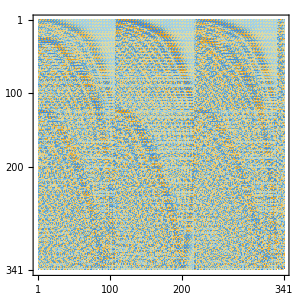

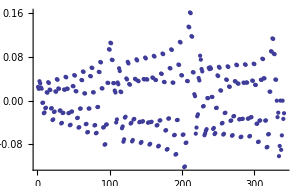

-0.0160281

-3.39745

{-72.2181,-66.8629,-62.1743,-61.9304,-61.0162,-60.796,-59.8912,-59.6823,-58.7823,-58.5808,-57.6836,-57.4878,-56.5921,-56.4014,-55.5061,-55.3205,-54.4245,-54.2442,-53.3464,-53.1721,-52.2711,-52.1037,-51.1979,-51.0385,-50.1264,-49.9762,-49.0562,-48.9161,-47.9868,-47.8576,-46.918,-46.8002,-45.8496,-45.7431,-44.7822,-44.6857,-43.7193,-43.6279,-42.7485,-42.5742,-42.468,-41.5433,-41.5007,-40.4774,-40.4383,-39.4051,-39.3725,-38.3302,-38.3041,-37.2535,-37.2332,-36.1751,-36.1599,-35.0955,-35.0842,-34.0149,-34.0059,-32.9342,-32.9248,-31.8536,-31.8414,-30.7739,-30.7565,-29.7012,-29.6709,-28.7635,-28.5863,-28.4451,-27.5145,-27.4773,-26.9365,-26.4001,-26.369,-25.5526,-25.5234,-25.3135,-25.2867,-24.3821,-24.3593,-24.2238,-24.2002,-23.2398,-23.2249,-23.1301,-23.1082,-22.1152,-22.107,-22.0299,-22.0086,-21.0046,-21.0014,-20.9218,-20.901,-19.904,-19.9026,-19.8082,-19.7879,-18.8094,-18.8054,-18.6929,-18.6723,-17.7163,-17.7094,-17.5775,-17.5556,-16.6232,-16.6135,-16.4626,-16.4385,-15.5298,-15.5173,-15.3482,-15.321,-14.4357,-14.4205,-14.2342,-14.203,-13.341,-13.3228,-13.1205,-13.0844,-12.2455,-12.2241,-12.0067,-11.9648,-11.1494,-11.1244,-10.8928,-10.8439,-10.0533,-10.0236,-9.77823,-9.72126,-8.958,-8.92151,-8.66275,-8.59616,-7.86658,-7.81817,-7.54566,-7.4678,-6.78973,-6.7136,-6.42593,-6.33655,-5.79359,-5.60798,-5.30168,-5.25631,-5.07862,-4.50187,-4.3888,-4.16823,-3.9819,-3.39745,-3.33767,-2.32451,-2.28271,-1.24121,-1.20881,-0.152056,-0.12512,0.94199,0.965646,2.04036,2.06207,3.14252,3.16317,4.24793,4.26811,5.35603,5.37615,6.46626,6.48662,7.40325,7.57815,7.59892,8.69106,8.71212,9.38115,9.79969,9.82872,9.86972,10.4722,10.9152,10.9447,11.0655,11.5098,12.0303,12.0585,12.236,12.5344,13.146,13.1704,13.3946,13.5811,14.2623,14.2818,14.5462,14.6583,15.3792,15.394,15.6931,15.7576,16.4968,16.5073,16.8365,16.8697,17.6149,17.6218,17.977,17.9887,18.7335,18.7374,19.1108,19.1154,19.852,19.8548,20.2346,20.2511,20.9697,20.9743,21.3583,21.3848,22.0875,22.0952,22.4813,22.5164,23.2055,23.2171,23.603,23.6458,24.3237,24.3401,24.7231,24.773,25.4418,25.4642,25.8414,25.8981,26.5592,26.5897,26.9582,27.0208,27.6753,27.7168,28.0737,28.1411,28.7888,28.8457,29.1889,29.2589,29.8981,29.9769,30.3055,30.3739,31.0009,31.1108,31.4263,31.4859,32.0949,32.2483,32.5557,32.5942,33.1784,33.391,33.6952,33.7037,34.2512,34.5422,34.7913,34.8831,35.3156,35.7133,36.3702,36.7745,37.396,37.8525,38.3745,38.9405,39.3197,40.0357,40.2888,41.1363,41.3108,42.2406,42.3731,43.3473,43.4588,44.4553,44.558,45.5635,45.665,46.6706,46.7771,47.7751,47.8926,48.8745,49.0103,49.9641,50.1297,51.0352,51.2503,52.0705,52.3718,53.0481,53.4936,53.9823,54.6157,54.9448,55.7374,55.9689,56.8581,57.0365,57.977,58.128,59.0922,59.2329,60.2003,60.3461,61.2942,61.4648,62.3583,62.5877,63.3624,63.7139,64.2934,64.8432,65.2335,65.9754,66.2538,67.1106,67.3352,68.2491,68.4506,69.3915,69.588,70.539,70.7458,71.6937,71.9352}

0.

```mathematica
(*Admixture of 60s1/2 at 500V/m*)
EField={0,0,500};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152,152]]
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152]]-Subscript[E, 12]/10^9
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]-Subscript[E, 12]/10^9
```

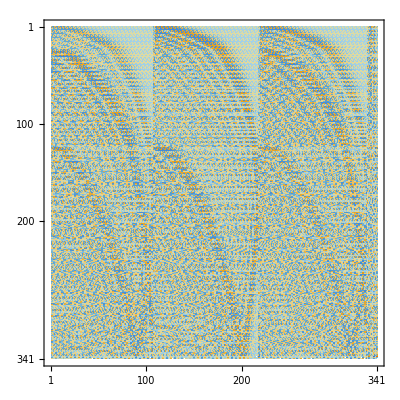

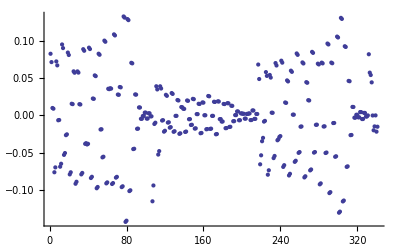

0.0478166

-13.5686

-7.79615

```mathematica
(*Admixture of 58d3/2 at 300V/m*)
EField={0,0,300};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114,114]]
EField={0,0,300};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
```

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```